# NG_4 T_01 ШпакАндрей. Многослойный персептрон

Искусственная нейросеть и логические операции. Реализуйте три разных нейросети небольшого размера, архитектуры которых приведены на Рис.1. В качестве функции активации используйте пороговую функцию UnitSteppaclet:ref/UnitStep. Математическая модель нейрона (нейросети kmANN21) описывается формулой (DisplayFormulaNumbered).

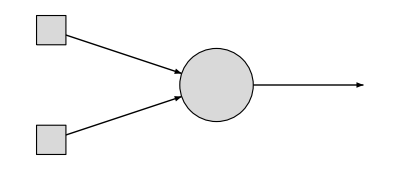
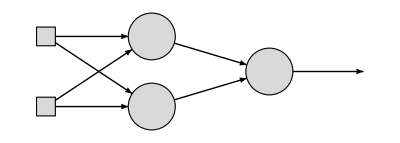
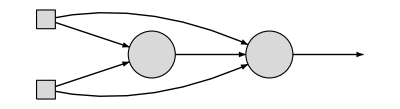
-Graphics-kmANN21 | -Graphics-kmANN221 | -Graphics-kmANN211
Рис 1. Искусственные нейросети

kmANN21_(W⃗)(x⃗):=UnitStep(w_1 x_1+w_2 x_2+w_0)

Решение:

-Graphics-

```mathematica
ClearAll[kmANN21,kmANN221,kmANN211];
kmANN21[W_?VectorQ]@{x1_,x2_}:=UnitStep[W.{x1,x2,1}];
kmANN221[{{W11_,W12_}?MatrixQ,W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{W11.{x1,x2,1},W12.{x1,x2,1},1}];
kmANN211[{W1_?VectorQ,W2_?VectorQ}]@{x1_,x2_}:=
```

# Как я разбирался с заданиями

1.

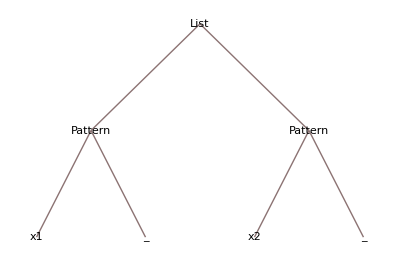

```mathematica
(*Вспоминаю про шаблоны с помощью TreeForm*)
{x1_,x2_}//TreeForm
```

```mathematica
(*Что такое префикс и для чего он нужен при работе в первом задании. Но так и не понял. ВОПРОС*)
Prefix[f@{z1, z2}]
```

f@{z1,z2}

```mathematica
{1, 2, 3}*{4,5,6}
```

{4,10,18}

```mathematica
Plus@@({1, 2, 3}*{4,5,6})
```

32

```mathematica
(*Можно и использовать Dot, это более лаконично*)
{1, 2, 3}.{4,5,6}
```

32

```mathematica
(*Разбираюсь со второй функцией kmANN221*)
W11={w1,w2}
x1*W11
```

{w1,w2}

{w1 x1,w2 x1}

```mathematica
x1.W11
```

x1.{w1,w2}

```mathematica
const=1
const.{w1,w2}
const.{1,2}
{const, const}.{w1,w2}
```

1

1.{w1,w2}

1.{1,2}

w1+w2

```mathematica
W12={w3,w4}
x1*W11
x2*W12
```

{w3,w4}

{w1 x1,w2 x1}

{w3 x2,w4 x2}

```mathematica
x1*W11[[1]]
x2*W12[[1]]
```

w1 x1

w3 x2

```mathematica
x1*W11[[2]]
x2*W12[[2]]
```

w2 x1

w4 x2

```mathematica
(x1*W11[[1]]).(x2*W12[[1]])
```

(w1 x1).(w3 x2)

```mathematica
(x1*W11[[2]]).(x2*W12[[2]])
```

(w2 x1).(w4 x2)

```mathematica
W2.{(x1*W11[[1]]).(x2*W12[[1]]),(x1*W11[[2]]).(x2*W12[[2]])}
```

W2.{(w1 x1).(w3 x2),(w2 x1).(w4 x2)}

```mathematica
(*Как мне казалось, я сделал правильно, но, пересматривая условие я понял, что сделал не так: забыл про w0 и перепутал весь принцип формирования линейной комбинации значений с весами. Поэтому заново и более внимательно и пошагово ещё раз.*)
```

```mathematica
W11={w1,w2,w0};
W12={w3,w4,w0};
W11.{x1,x2,1}
W12.{x1,x2,1}
```

w0+w1 x1+w2 x2

w0+w3 x1+w4 x2

```mathematica
W2={w5,w6,w0};
W2.{W11.{x1,x2,1},W12.{x1,x2,1},1}
```

w0+w5 (w0+w1 x1+w2 x2)+w6 (w0+w3 x1+w4 x2)

```mathematica
(*Остается добавить только UnitStep*)
```

```mathematica
(*Разбираюсь с третьей функцией kmANN211, снова пошагово*)
-Graphics-
```